```mathematica
Table[(-1)^Random[Integer],{10}]
```

{1,-1,1,-1,1,-1,-1,-1,-1,1}

```mathematica
FoldList[Plus,0,%]
```

{0,1,0,1,0,1,0,-1,-2,-3,-2}

```mathematica
walk1D[n_]:=
FoldList[Plus,0,Table[(-1)^Random[Integer],{n}]]
```

```mathematica
walk1D[10]
```

{0,-1,-2,-1,0,-1,-2,-1,-2,-1,0}

```mathematica
NestList[(#+(-1)^Random[Integer])&,0,n]
```

NestList::intnm: Non-negative machine-sized integer expected at position 3 in NestList[#1+(-1)^Random[Integer]&,0,n].

NestList[#1+(-1)^Random[Integer]&,0,n]

```mathematica
{{0,1},{1,0},{0,-1},{-1,0}}[[Table[Random[Integer,{1,4}],{n}]]]
```

Table::iterb: Iterator {n} does not have appropriate bounds.

Part::pkspec1: The expression Table[Random[Integer,{1,4}],{n}] cannot be used as a part specification.

{{0,1},{1,0},{0,-1},{-1,0}}⟦Table[Random[Integer,{1,4}],{n}]⟧

```mathematica
Walk2D[n_]:=FoldList[Plus,{0,0},
{{0,1},{1,0},{0,-1},{-1,0}}[[
Table[Random[Integer,{1,4}],{n}]]]]
```

```mathematica
Walk2D[10]
```

{{0,0},{1,0},{1,1},{1,2},{1,1},{2,1},{2,0},{1,0},{1,1},{1,0},{1,1}}

```mathematica
ShowWalk2D[coords_,opts___]:=
Show[Graphics[Line[coords],
opts,
AspectRatio->Automatic]]
```

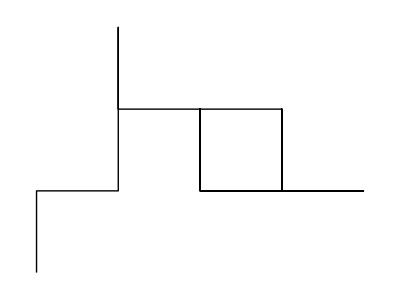

```mathematica
ShowWalk2D[Walk2D[20]]
```

```mathematica
walk=Walk2D[10]
```

{{0,0},{0,-1},{0,-2},{0,-1},{0,-2},{0,-1},{0,0},{1,0},{2,0},{2,1},{1,1}}

```mathematica
Map[{Min[#],Max[#]}&,Transpose[walk]]
```

{{0,2},{-2,1}}

```mathematica
AnimateWalk2D[coords_,opts___]:=
Map[Show[Graphics[Line[Take[coords,#]]],
opts,AspectRatio->Automatic,
PlotRange->Map[{Min[#],Max[#]}&,
Transpose[walk]]]&,
Range[2,Length[coords]]]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

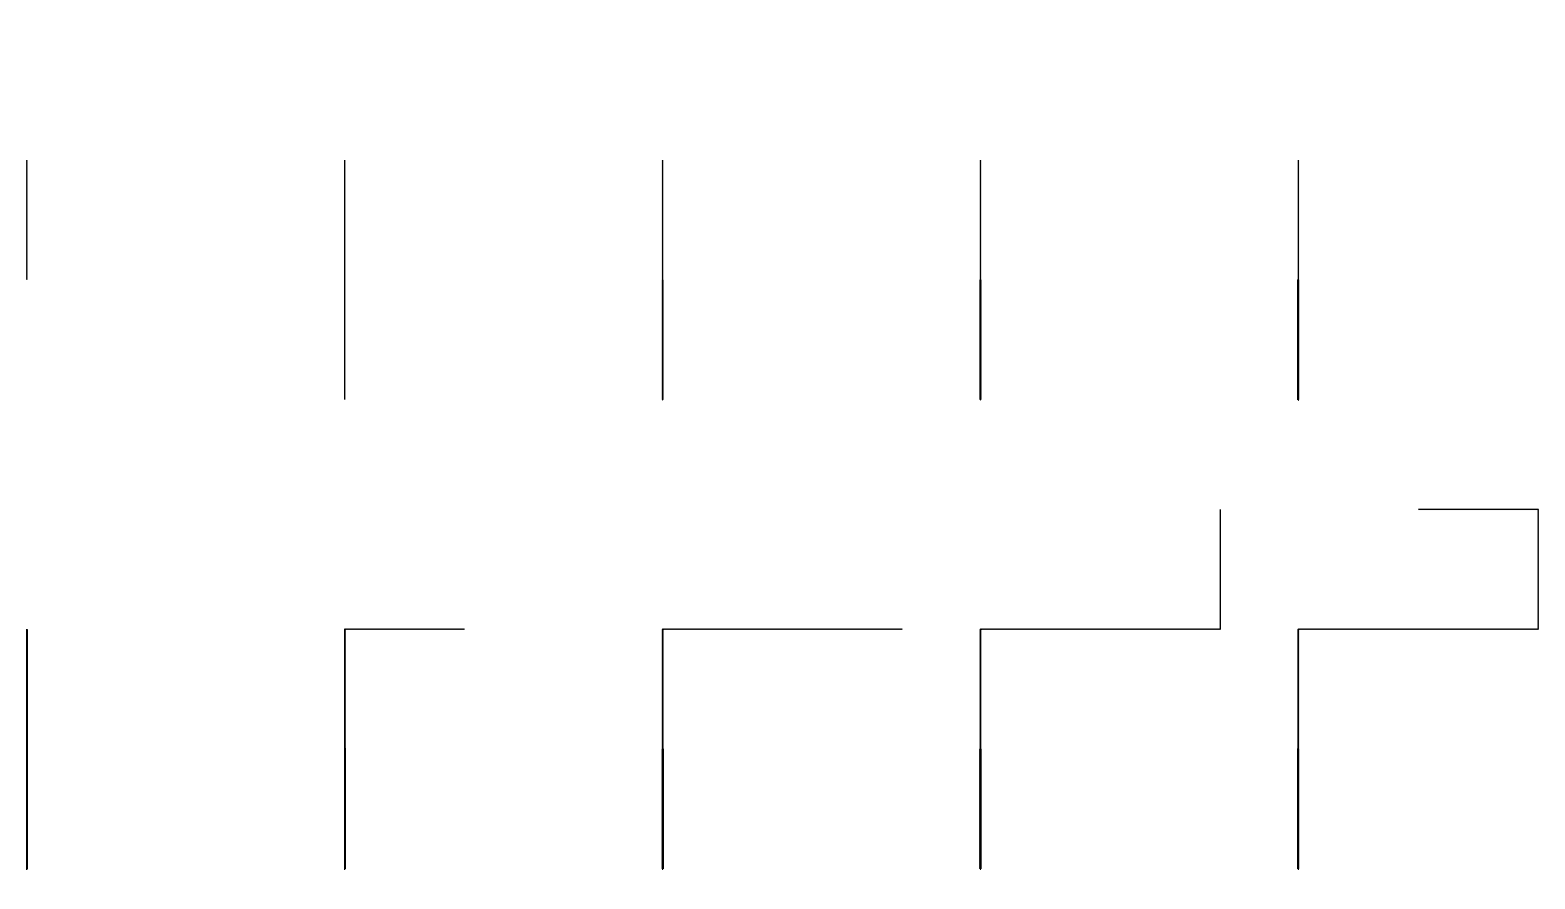

```mathematica
Show[GraphicsArray[Partition[AnimateWalk2D[walk,DisplayFunction->Identity],5]]]
```

```mathematica
SquareDistance[walk_List]:=Apply[Plus,Last[walk]^2]
```

```mathematica
SquareDistance[walk]
```

2

```mathematica
MeanSquareDistance[n_Integer,m_Integer]:=
Module[{walk2D},
walk2D[s_]:=
FoldList[Plus,{0,0},
{{0,1},{1,0},{0,-1},{-1,0}}[[
Table[Random[Integer,{1,4}],{s}]]]];
N[Sum[Apply[Plus,Last[walk2D[n]]^2],{m}]/m]
]
```

```mathematica
MeanSquareDistance[10,25]
```

9.52

```mathematica
MeanSquareRadiusGyration[m_Integer,n_Integer]:=
Module[{squareRadiusGyration},
squareRadiusGyration[s_Integer]:=
Module[{locs,cm,choices={{1,0},{-1,0},{0,1},{0,-1}}},
locs=FoldList[Plus,{0,0},
choices[[Table[Random[Integer,{1,4}],{s}]]]];
cm=N[Apply[Plus,locs]/(s+1)];
Apply[Plus,Flatten[(Transpose[locs]-cm)^2]]/(s+1)
];
N[Sum[squareRadiusGyration[n],{m}]/m]
]
```

```mathematica
MeanSquareRadiusGyration[15,20]
```

3.24142

```mathematica
data=Map[({MeanSquareDistance[#,75],#})&,
Range[10,90,20]]
```

{{9.73333,10},{27.4133,30},{57.0133,50},{88.96,70},{78.4267,90}}

```mathematica
calculatedExponent=Fit[N[Log[data]],{x},x]
```

0.990985 x

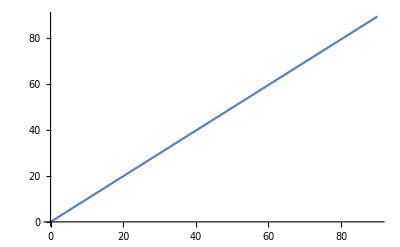

```mathematica
calculatedGraph=Plot[calculatedExponent,{x,0,90}]
```

```mathematica
Needs["Graphics`Graphics`"]
```

Get::noopen: Cannot open Graphics`Graphics`.

Needs::nocont: Context Graphics`Graphics` was not created when Needs was evaluated.

$Failed

```mathematica
dataGraph=LogLogListPlot[data,PlotStyle->PointSize[.03]]
```

LogLogListPlot[{{9.73333,10},{27.4133,30},{57.0133,50},{88.96,70},{78.4267,90}},PlotStyle→PointSize[0.03]]

```mathematica
Show[dataGraph,calculatedGraph]
```

Show::gcomb: Could not combine the graphics objects in Show[LogLogListPlot[{{9.73333,10},{27.4133,30},{57.0133,50},{88.96,70},{78.4267,90}},PlotStyle→PointSize[0.03]],].

Show[LogLogListPlot[{{9.73333,10},{27.4133,30},{57.0133,50},{88.96,70},{78.4267,90}},PlotStyle→PointSize[0.03]],-Graphics-]

```mathematica
Walk3D[n_]:=FoldList[Plus,{0,0,0},
{{-1,1,1},{-1,-1,1},{1,-1,1},{1,1,1},
{-1,1-1},{-1,-1,-1},{1,-1,-1},{1,1,-1}}[[
Table[Random[Integer,{1,8}],{n}]]]]
```

```mathematica
OffLattice[n_]:=
FoldList[Plus,{0.0,0.0},
Map[{Cos[#],Sin[#]}&,
Table[Random[Real,{0,N[2Pi]}],{n}]]]
```

```mathematica
AnimateWalk2D[coords_,opts___]:=
Map[Show[Graphics[{
{RGBColor[1,0,0],PointSize[.02],
Point[coords[[#]]]},
Line[Take[coords,#]]}],
opts,
AspectRatio->Automatic,
PlotRange->Map[{Min[#]-.2,Max[#]+.2}&,
Transpose[coords]]]&,
Range[2,Length[coords]]]
```